```mathematica
ρ0=1;
L1=12;
L2=12;
γ=1.4;
c=1.4;
eps=0.001;
alphaa=2;
initrho[r_]:=eps Exp[-alphaa r^2]
```

```mathematica
NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]
```

NIntegrate::inumr: The integrand initrho[x,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4},{0,4}}.

NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]

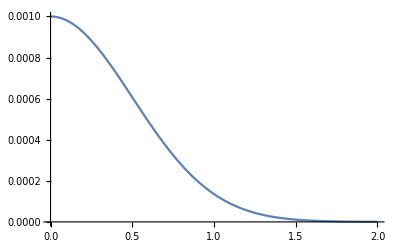

```mathematica
Plot[initrho[r],{r,0,2}]
```

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=eps/(2alphaa)NIntegrate[Exp[-ξ^2/(4alphaa)]Cos[ξ t]BesselJ[0,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
uAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(x-L1/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
vAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(y-L2/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
mcrCenterLine=MeshCellRcm[[nx ny/2+1;;nx ny/2+nx]];
```

```mathematica
mmm=Table[mcrCenterLine[[i]],{i,mcrCenterLine//Length}];
```

```mathematica
rhoAn[mmm[[1,1]],mmm[[1,2]],2.0]
```

2.45034×10^-17

```mathematica
timeP = 20.0;
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

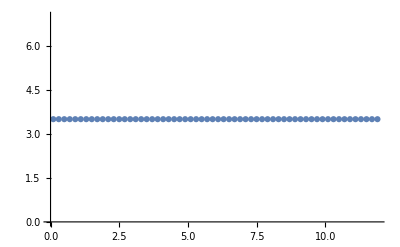

```mathematica
dataExact=ListPlot[dataAnCenterH,PlotRange->All]
```

```mathematica
dataAnCenter[[1]]
```

NIntegrate::inumr: The integrand ⅇ^(-1/8 (0.+ξ)^2) (0.+ξ) BesselJ[0,(0.+ξ) √(({«400»}⟦{«2»},1⟧)^2+({«400»}⟦{«2»},2⟧)^2)] Cos[2. ξ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
rho[1,0.2]
```

1.40039

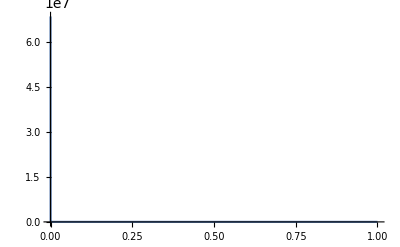

```mathematica
Plot[rho[rr,0.2],{rr,0,1},PlotRange->All]
```